```mathematica
(*Capacitante function parameters*)
SetDirectory[NotebookDirectory[]];
α = 0.3;C0=0.5;T=1; θ1=3*T;θ2=3*T;
(*FHN Parameters*)
ep=0.08;β=0.8;γ=0.7;maxtime=50;
Ct[t_]=Which[Mod[t,T]<α T,1,Mod[t,T]<α T+(1-C0)/θ1,1-(Mod[t,T]-α T)θ1, Mod[t,T]<T-(1-C0)/θ2,C0, True,C0+(Mod[t,T]-T+(1-C0)/θ2)θ2];
Ctd[t_]=Which[Mod[t,T]<α T,0,Mod[t,T]<α T+(1-C0)/θ1,-θ1, Mod[t,T]<T-(1-C0)/θ2,0, True,θ2];
```

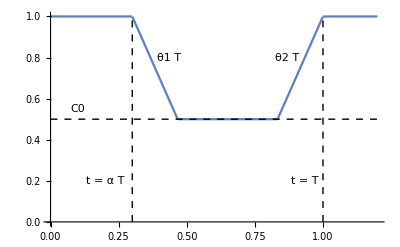

Fig1.png

```mathematica
CC[t_]=Which[t< α T,1,t<α T+(1-C0)/θ1,1-(t- α T) θ1,t<T-(1-C0)/θ2,C0,True,C0 + (t-T+(1-C0)/θ2)θ2];
g1 = Plot[{CC[Mod[t,T]]},{t,0,1.2*T},PlotRange->{0,1},PlotLegends->Placed[StringJoin["C0=",ToString[C0],", T=",ToString[T],", θ1=",ToString[θ1],", θ2=",ToString[θ2]],Above]];
g2 = Graphics[{Dashed, Line[{{α T,0},{α T,1}}]}];

g3 = Graphics[{Text["t = α T",{α T -0.1,0.2}]}];
g4 = Graphics[{Text["θ1 T",{13/30*T,0.8}],Text["θ2 T",{26/30T,0.8}]}];
g5 = Graphics[{Dashed, Line[{{T,0},{T,1}}]}];
g6 = Graphics[{Text["t = T",{28/30,0.2}]}];
g7 = Graphics[{Dashed, Line[{{0,C0},{1.2T,C0}}]}];
g8 = Graphics[{Text["C0",{0.1 T,0.55}]}];

export = Show[g1,g2,g3,g4,g5,g6,g7,g8]
Export["Fig1.png",export]
```